Mohamed M. Hammad

Neural Network and Deep Learning with Mathematica                              <    Ξ

Edited by Hao Feng

## 10 Complex Valued Neural Networks

Remark:
This chapter provides a Mathematica implementation of the concepts and ideas presented in Chapter 9, [1], of the book titled Artificial Neural Network and Deep Learning: Fundamentals and Theory. We strongly recommend that you begin with the theoretical chapter to build a solid foundation before exploring the corresponding practical implementation. This chapter also serves as a summary of the article titled  Comprehensive Survey of Complex- Valued Neural Networks: Insights into Backpropagation and Activation Functions. For more details about complex valued activation functions, please refer to Ref [39].

In this chapter, we delve into the world of complex-valued activation functions (CVAFs) and their visualizations using Mathematica. For a more comprehensive background, we refer to [39] and the references cited therein. The ability to visualize these functions is crucial for gaining deeper insights into their behavior and understanding how they transform complex inputs. By leveraging Mathematica’s powerful visualization tools, we can explore the intricacies of CVAFs in both two-dimensional and three-dimensional representations.

Three-dimensional plots are particularly useful for visualizing the magnitude and phase of complex functions. Mathematica’s ComplexPlot3D function is designed to generate a three-dimensional representation of the magnitude of the function, Abs[f], while using color to indicate the argument, Arg[f], over a specified complex rectangle. This type of plot provides a comprehensive view, allowing us to observe how the magnitude and phase of a CVAF vary across the complex plane. We will demonstrate how to use ComplexPlot3D effectively to visualize various CVAFs, providing detailed examples and techniques to enhance your understanding. These visualizations are invaluable for analyzing the behavior of CVAFs, revealing patterns and characteristics that are not immediately apparent from the mathematical formulation alone.

While three-dimensional plots offer a detailed perspective, two-dimensional visualizations are often more accessible and easier to interpret for certain applications. The ComplexPlot function in Mathematica generates a two- dimensional representation of Arg[f] over the complex rectangle, effectively mapping the phase of the function onto a color gradient. This straightforward visualization technique is powerful for quickly assessing the function’s behavior on the complex plane. Throughout this chapter, we will explore how to utilize ComplexPlot to visualize CVAFs, offering practical examples and tips for creating clear and informative plots. These two-dimensional visualizations complement the three-dimensional ones, providing a different yet equally valuable perspective on the behavior of CVAFs.

Interactivity is a key feature in Mathematica that allows for dynamic exploration of CVAFs. Using the `Manipulate` function, we can create interactive visualizations where the parameters of the AFs can be adjusted in real-time. This dynamic approach enables us to observe how changes in parameters affect the AFs, offering a hands-on way to explore their behavior. Interactive simulations and visualizations facilitate a deeper understanding of the mathematical underpinnings of CVAFs.

To provide a comprehensive resource, this chapter includes an extensive catalog of CVAFs, detailing their definitions, properties, and visual representations. The catalog covers a wide range of AFs, including but not limited to: Split-Step Function, Split-Sigmoid, Split-Parametric Sigmoid, Split-Tanh, Split-Sigmoid Tanh, Split-Hard Tanh, Split-CReLU, Split-QAM, Amplitude-Phase-Type Function, Amplitude-Phase Sigmoidal Function, Complex Cardioid, modReLU, Fully Complex Tanh, Fully Complex Logistic-Sigmoidal, Fully Complex Elementary Transcendental Function (ETF), zReLU, z3ReLU, zPReLU, z3PreLU.

### Complex Numbers and Functions

code 10.1

(* The code defines complex variables and functions, separates their real and imaginary parts, and visualizes these components using contour plots. Specifically, it creates a complex function f by squaring a complex variable z, then defines u and v as the real and imaginary parts of f respectively. It plots the contours of u and v for specified values in the uv-plane and also plots hyperbolas defined by x^2-y^2=c1 and 2xy=c2 in the xy-plane, providing a graphical representation of these mathematical relationships: *)

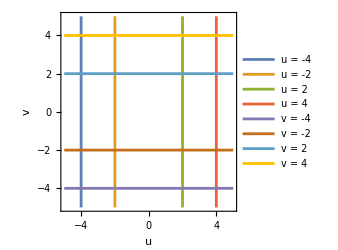

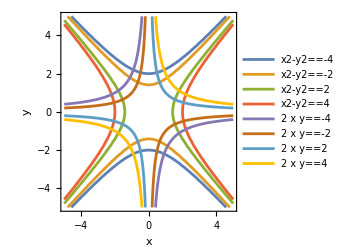

```mathematica
z[x_,y_]:=x+I y

f[x_,y_]:=z[x,y]^2

u[x_,y_]:=Re[f[x,y]]

v[x_,y_]:=Im[f[x,y]]

c1Values={-4,-2,2,4};

c2Values={-4,-2,2,4};

ContourPlot[{u==-4,u==-2,u==2,u==4,v==-4,v==-2,v==2,v==4},{u,-5,5},{v,-5,5},FrameLabel->{"u","v"},PlotLegends->{"u = -4","u = -2","u = 2","u = 4","v = -4","v = -2","v = 2","v =
4"},PlotRange->All,ImageSize->250]

ContourPlot[{x^2-y^2==-4,x^2-y^2==-2,x^2-y^2==2,x^2-y^2==4,2 x y==-4,2 x y==-2,2 x y==2,2 x y==4},{x,-5,5},{y,-5,5},FrameLabel->{"x","y"},PlotLegends->{"x2-y2==-4","x2-y2==-2","x2-y2==2","x2-y2==4","2 x y==-4","2 x
y==-2","2 x y==2","2 x y==4"},PlotRange->All,ImageSize->250]
```

code 10.2

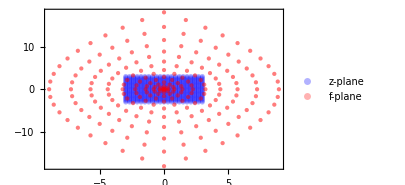

```mathematica
f[z_]:=z^2

getRealImag[expr_]:={Re[expr],Im[expr]}

gridPoints=Flatten[Table[{x,y},{x,-3,3,0.3},{y,-3,3,0.3}],1];

mappedPoints=f[MapApply[Complex,gridPoints]];

mappedRealImag=Map[getRealImag,mappedPoints];

ListPlot[
{gridPoints,mappedRealImag},PlotStyle->{Directive[PointSize[0.012],Blue,Opacity[0.3]],Directive[PointSize[0.01],Red,Opacity[0.3]]},Frame->True,PlotRange->Full,PlotLegends->{"z-plane","f-plane"},ImageSize->300
]
```

code 10.3

(* In this code, the Manipulate function allows you to interactively change the exponent in the complex mapping function f(z)=z^exp. The slider labeled “Exponent” allows you to dynamically adjust the value of exp, and the plot updates accordingly: *)

```mathematica
Manipulate[f[z_]:=z^exp;
getRealImag[expr_]:={Re[expr],Im[expr]};
gridPoints=Flatten[Table[{x,y},{x,-3,3,0.3},{y,-3,3,0.3}],1];
mappedPoints=f[MapApply[Complex,gridPoints]];
mappedRealImag=Map[getRealImag,mappedPoints];
ListPlot[{gridPoints,mappedRealImag},PlotStyle->{Directive[PointSize[0.012],Blue,Opacity[0.3]],Directive[PointSize[0.01],Red,Opa city[0.3]]},Frame->True,PlotRange->Full,PlotLegends->{"z-plane","f-plane"},ImageSize->300],
{{exp,2,"Exponent"},0.1,3,0.1}
]
```

code 10.4

(* The code visualizes and analyzes complex functions by transforming a grid of points in the complex plane using the functions f(z)=z^2 and f(z)= 1/z, and plotting the results. It generates the original grid and its transformations, converts complex numbers to pairs of real coordinates for plotting, and creates 3D plots of the magnitude and argument of the functions. Finally, it displays these visualizations in a grid layout, allowing for easy comparison and exploration of how the complex functions affect the plane: *)

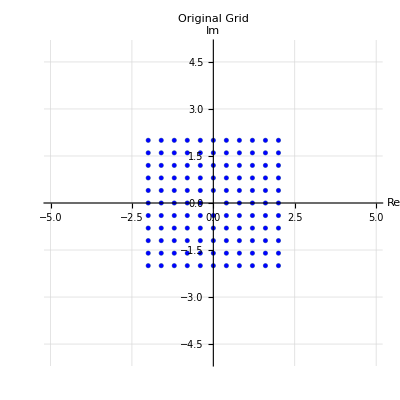
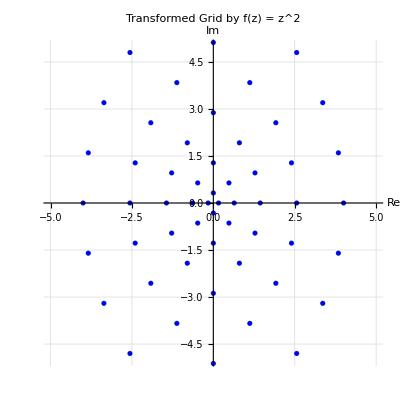
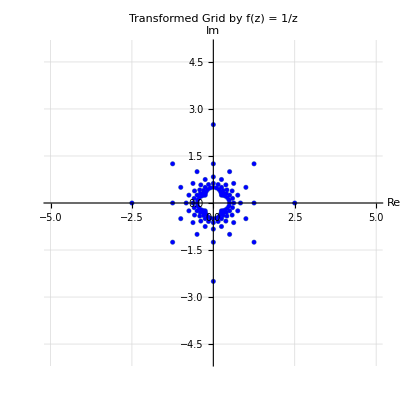
-Graphics- | -Graphics- | -Graphics- | 
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
f1[z_]:=z^2

f2[z_]:=If[z==0,Infinity,1/z]

gridPoints=DeleteCases[Flatten[Table[x+I y,{x,-2,2,0.4},{y,-2,2,0.4}]],0+0. I];

transformedGrid1=gridPoints/. z_Complex:>f1[z];

transformedGrid2=gridPoints/. z_Complex:>f2[z];
toRealPairs[complexList_]:={Re[#],Im[#]}&/@complexList

plotGrid[points_,title_]:=ListPlot[toRealPairs[points],AxesOrigin->{0,0},AspectRatio->1,PlotRange->{{-5,5},{-5,5}},GridLines->Automatic,Epilog->{Blue,PointSize[Medium],Point[toRealPairs[points]]},AxesLabel->{"Re","Im"},PlotLabel->title];

plotMagnitudeAndArgument[f_,range_,title_]:=Module[{magnitude,argument},magnitude=Plot3D[Abs[f[x+I y]],{x,-range,range},{y,-range,range},PlotRange->All,ColorFunction->"Rainbow",MeshFunctions->{#3&},MeshStyle->Gray,PlotLabel->"Magnitude: "<>title,AxesLabel->{"Re","Im","|f(z)|"}];
argument=Plot3D[Arg[f[x+I y]],{x,-range,range},{y,-range,range},PlotRange->{-Pi,Pi},ColorFunction->"Rainbow",MeshFunctions->{#3&},MeshStyle->Gray,PlotLabel->"Argument: "<>title,AxesLabel->{"Re","Im","Arg(f(z))"}];
{magnitude,argument}];

gridPlotOriginal=plotGrid[gridPoints,"Original Grid"];

gridPlotTransformed1=plotGrid[transformedGrid1,"Transformed Grid by f(z) = z^2"];

gridPlotTransformed2=plotGrid[transformedGrid2,"Transformed Grid by f(z) = 1/z"];

{magPlot1,argPlot1}=plotMagnitudeAndArgument[f1,2,"f(z) = z^2"];

{magPlot2,argPlot2}=plotMagnitudeAndArgument[f2,2,"f(z) = 1/z"];
Grid[{{gridPlotOriginal,gridPlotTransformed1,gridPlotTransformed2},{magPlot1,argPlot1,magPlot2,argPlot2}},Frame->All]
```

code 10.5

(* The code aims to visualize and interactively explore the impact of parameters on the transformations of a complex plane grid by two parameterized complex functions (f(z)=(a z)^2+b and f(z)= c/z+d. It generates a grid of complex points, excluding the origin, converts these points to real coordinate pairs for plotting, and uses `Manipulate` to allow dynamic adjustment of the parameters a, b, c, and d: *)

```mathematica
f1[z_,a_,b_]:=(a z)^2+b
f2[z_,c_,d_]:=If[z==0,Infinity,c/z+d] 
gridPoints=DeleteCases[Flatten[Table[x+I y,{x,-2,2,0.4},{y,-2,2,0.4}]],0+0. I];

toRealPairs[complexList_]:={Re[#],Im[#]}&/@complexList

plotGrid[points_,title_]:=ListPlot[toRealPairs[points],AxesOrigin->{0,0},AspectRatio->1,PlotRange->{{-5,5},{-5,5}},GridLines->Automatic,Epilog->{Blue,PointSize[Medium],Point[toRealPairs[points]]},AxesLabel->{"Re","Im"},ImageSize->250,PlotLabel->title];

Manipulate[Module[{transformedGrid1,transformedGrid2,gridPlotOriginal,gridPlotTransformed1,gridPlotTransformed2},transformedGrid1=gridPoints/. z_Complex:>f1[z,a,b];
transformedGrid2=gridPoints/. z_Complex:>f2[z,c,d];
gridPlotOriginal=plotGrid[gridPoints,"Original Grid"];
gridPlotTransformed1=plotGrid[transformedGrid1,"Transformed Grid by f(z) = (a
z)^2 + b"];
gridPlotTransformed2=plotGrid[transformedGrid2,"Transformed Grid by f(z) = c/z
+ d"];
Grid[{{gridPlotOriginal,gridPlotTransformed1,gridPlotTransformed2}},Frame->All]],{{a,1,"a"},-2,2,0.1},{{b,0,"b"},-2,2,0.1},{{c,1,"c"},-2,2,0.1},{{d,0,"d"},-2,2,0.1}]
```

code 10.6

```mathematica
AbsArgPlot[Sin[I x]+Sin[Pi x],{x,-2,2},PlotRange->Full,PlotLegends->Automatic,ImageSize->250]
```

-Graphics-

code 10.7

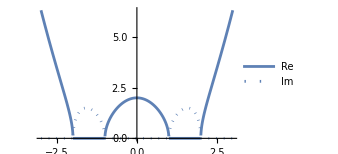

```mathematica
ReImPlot[Sqrt[(x^2-1) (x^2-4)],{x,-3,3},PlotRange->Full,PlotLegends->Automatic,ImageSize->250]
```

code 10.8

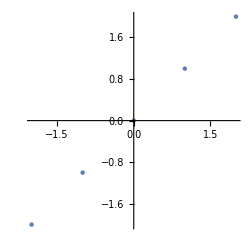

```mathematica
ComplexListPlot[{-2-2 I,-1-I,0,1+I,2+2 I},PlotRange->Full,ImageSize->250]
```

code 10.9

```mathematica
ComplexPlot3D[(z^4-1)/z^2,{z,-2-2 I,2+2 I},ColorFunction->"CyclicLogAbs",PlotLegends->Automatic,ImageSize->300]
```

-Graphics3D-

code 10.10

```mathematica
ComplexPlot3D[(z^4-1)/z^2,{z,-2-2 I,2+2 I},ColorFunction->"CyclicArg",PlotLegends->Automatic,ImageSize->300]
```

-Graphics3D-

code 10.11

```mathematica
ComplexPlot3D[(z^4-1)/z^2,{z,-2-2 I,2+2 I},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,ImageSize->300]
```

-Graphics3D-

code 10.12

```mathematica
ComplexPlot3D[(z^4-1)/z^2,{z,-2-2 I,2+2 I},ColorFunction->"QuantileAbs",PlotLegends->Automatic,ImageSize->300
]
```

-Graphics3D-

code 10.13

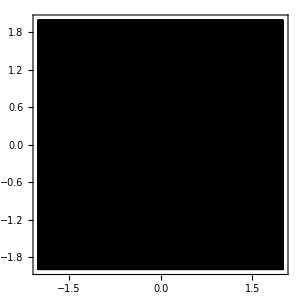

```mathematica
ComplexPlot[(z^4-1)/z^2,{z,-2-2 I,2+2 I},ColorFunction->{Automatic,"CyclicLogAbs"},PlotLegends->Automatic,ImageSize->300]
```

code 10.14

```mathematica
ComplexPlot[(z^4-1)/z^2,{z,-2-2 I,2+2 I},ColorFunction->"CyclicArg",PlotLegends->Automatic,ImageSize->300]
```

-Graphics-

code 10.15

```mathematica
ComplexPlot[(z^4-1)/z^2,{z,-2-2 I,2+2 I},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,ImageSize->300]
```

-Graphics-

code 10.16

```mathematica
ComplexPlot[(z^4-1)/z^2,{z,-2-2 I,2+2 I},ColorFunction->"QuantileAbs",PlotLegends->Automatic,ImageSize->300]
```

-Graphics-

code 10.17

(* The code allows the user to choose a complex-valued function f from a predefined set of options. The options include real and complex parts (Re,Im),magnitude (Abs),argument (Arg),and various transcendental functions (Sin, Cos, Tan, Log, Tanh, ArcSinh, ArcTanh, Sqrt, Gamma). Two types of complex plots are displayed side by side within a Row.The first plot is a 2D complex plot (ComplexPlot) using the chosen function f(z).It uses the color function “QuantileAbs” and includes legends. The second plot is a 3D complex plot (ComplexPlot3D) using the same function and a different color function (“CyclicLogAbs”).It also includes legends and has a specified plot range. The Manipulate function provides an interactive interface, allowing the user to dynamically manipulate the displayed plots by selecting different functions for f: *)

```mathematica
Manipulate[Row[{ComplexPlot[f[z],{z,-2-2 I,2+2 I},ColorFunction->"QuantileAbs",PlotLegends->Automatic,ImageSize->300],ComplexPlot3D[f[z],{z,-2-2 I,2+2 I},ColorFunction->"CyclicLogAbs",PlotRange->Full,PlotLegends->Automatic,ImageSize->300]}],{{f,Tanh},{Re,Im,Abs,Arg,Sin,Cos,Tan,Log,Tanh,ArcSinh,ArcTanh,Sqrt,Gamma}},ControlType->SetterBar]
```

### Complex Valued Activation Functions

code 10.18

(* The code defines and visualizes the Split-Step activation function for a complex variable z=x+iy by applying the step function separately to its real and imaginary parts. It introduces a modular function `createSplitStepPlot` to generate and display 3D surface plots and slice contour plots for the real part, imaginary part, magnitude, and phase of the Split-Step function. The generated plots are displayed together, allowing for a comprehensive examination of the Split-Step function’s behavior across different components in the complex plane: *)

```mathematica
createSplitStepPlot[component_,label_]:=Module[{plot1,slice},(*Define a complex variable:*)znumber=x+I*y;
σSSF[u_]:=If[u>=0,1,0];
σSplitStep:=σSSF[Re[znumber]]+I σSSF[Im[znumber]];
plot1=Plot3D[component,{x,-6,6},{y,-6,6},ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"];
slice=SliceContourPlot3D[component,z==0,{x,-6,6},{y,-6,6},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"];
Show[plot1,slice,PlotRange->All,PlotLabel->label,BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->200]]

realSplitStepPlot=createSplitStepPlot[Re[σSplitStep],"Real Part of Split-StepF(z)"];
imaginarySplitStepPlot=createSplitStepPlot[Im[σSplitStep],"Imaginary Part of Split-StepF(z)"];
magnitudeSplitStepPlot=createSplitStepPlot[Abs[σSplitStep],"Magnitude of Split-StepF(z)"];
phaseSplitStepPlot=createSplitStepPlot[Arg[σSplitStep],"Phase of Split-StepF(z)"];

{realSplitStepPlot,imaginarySplitStepPlot,magnitudeSplitStepPlot,phaseSplitStepPl ot}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,ot phaseSplitStepPl}

code 10.19

-Graphics3D-

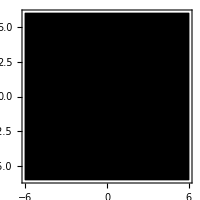

```mathematica
σSSF[u_]:=If[u>=0,1,0];
σSplitStep:=σSSF[Re[z]]+I σSSF[Im[z]];

ComplexPlot3D[σSplitStep,{z,-6-6 I,6+6 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","σSplitStep(z)"},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->270]

ComplexPlot[σSplitStep,{z,-6-6 I,6+6 I},PlotRange->All,ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200]
```

code 10.20

(* The code defines and visualizes the split-sigmoidal activation function for a complex variable z=x+iy by applying the sigmoid function separately to its real and imaginary parts. It introduces a modular function `createSplitSigmoidalPlot` to generate and display 3D surface plots and slice contour plots for the real part, imaginary part, magnitude, and phase of the split-sigmoidal function. The generated plots are displayed together, allowing for a comprehensive examination of the split-sigmoidal function’s behavior across different components in the complex plane: *)

```mathematica
createSplitSigmoidalPlot[component_,label_]:=Module[{plot1,slice},
znumber=x+I*y;

sigmoidalR[u_]:=1/(1+Exp[-u]);
splitsigmoidal:=sigmoidalR[Re[znumber]]+I sigmoidalR[Im[znumber]];

plot1=Plot3D[component,{x,-6,6},{y,-6,6},ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"];

slice=SliceContourPlot3D[component,z==0,{x,-6,6},{y,-6,6},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"];

Show[plot1,slice,PlotRange->All,PlotLabel->label,BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->200]
]

realSplitSigmoidalPlot=createSplitSigmoidalPlot[Re[splitsigmoidal],"Real Part of split-sigmoidalF(z)"];
imaginarySplitSigmoidalPlot=createSplitSigmoidalPlot[Im[splitsigmoidal],"Imaginary Part of split-sigmoidalF(z)"];
magnitudeSplitSigmoidalPlot=createSplitSigmoidalPlot[Abs[splitsigmoidal],"Magnitude of split-sigmoidalF(z)"
];
phaseSplitSigmoidalPlot=createSplitSigmoidalPlot[Arg[splitsigmoidal],"Phase of split-sigmoidalF(z)"];

{realSplitSigmoidalPlot,imaginarySplitSigmoidalPlot,magnitudeSplitSigmoidalPlot,p haseSplitSigmoidalPlot}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,haseSplitSigmoidalPlot p}

code 10.21

```mathematica
sigmoidalR[u_]:=1/(1+Exp[-u]);
splitsigmoidal:=sigmoidalR[Re[z]]+I sigmoidalR[Im[z]];

ComplexPlot3D[splitsigmoidal,{z,-6-6 I,6+6 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","splitSigmoidal(z)"},
ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->270
]

ComplexPlot[splitsigmoidal,{z,-6-6 I,6+6 I},PlotRange->All,ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200]
```

-Graphics3D-

-Graphics-

code 10.22

(* The code defines a function `createSplitPSigmoidalPlot` to visualize various components (real part, imaginary part, magnitude, and phase) of the Split- Parametric Sigmoidal CVAF (Complex-Valued Activation Function),which applies a parametric sigmoidal function separately to the real and imaginary parts of the complex variable z=x+iy. By modularly generating 3D surface plots and slice contour plots for each component over the range [-6,6] for both real and imaginary parts, the function combines these plots for comprehensive visualization. This approach efficiently produces and displays plots for the real part, imaginary part, magnitude, and phase of the Split-Parametric Sigmoidal CVAF, allowing for a detailed comparison and understanding of its behavior in the complex plane: *)

```mathematica
c1=0.7;
c2=3;

createSplitPSigmoidalPlot[component_,label_]:=Module[{plot1,slice},znumber=x+I*y;
σSPSigmoidalR[znumber_,c1_,c2_]:=(2 c1)/(1+Exp[-c2 znumber])-c1;
σSPSigmoidal:=σSPSigmoidalR[x,c1,c2]+I σSPSigmoidalR[y,c1,c2];
plot1=Plot3D[component,{x,-6,6},{y,-6,6},ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"];

slice=SliceContourPlot3D[component,z==0,{x,-6,6},{y,-6,6},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"];

Show[plot1,slice,PlotRange->All,PlotLabel->label,BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->200]
]

realSplitPSigmoidalPlot=createSplitPSigmoidalPlot[Re[σSPSigmoidal],"Real Part of split-PsigmoidF(z)"];
imaginarySplitPSigmoidalPlot=createSplitPSigmoidalPlot[Im[σSPSigmoidal],"Imaginary Part of split-PsigmoidF(z)"];
magnitudeSplitPSigmoidalPlot=createSplitPSigmoidalPlot[Abs[σSPSigmoidal],"Magnitude of split-PsigmoidF(z)"];
phaseSplitPSigmoidalPlot=createSplitPSigmoidalPlot[Arg[σSPSigmoidal],"Phase of split-PsigmoidF(z)"];
{realSplitPSigmoidalPlot,imaginarySplitPSigmoidalPlot,magnitudeSplitPSigmoidalPlo t,phaseSplitPSigmoidalPlot}
```

{-Graphics3D-,-Graphics3D-,magnitudeSplitPSigmoidalPlo t,-Graphics3D-}

code 10.23

(* This Manipulate allows you to dynamically adjust the values of c1 and c2 using sliders, providing an interactive way to observe the changes in the 3D plot and ContourPlot of the Magnitude of the Split-Parametric Sigmoidal CVAF: *)

```mathematica
Manipulate[Module[{plot1,slice,x,y},znumber=x+I*y;
σSPSigmoidalR[znumber_,c1_,c2_]:=(2 c1)/(1+Exp[-c2 znumber])-c1;
σSPSigmoidal:=σSPSigmoidalR[x,c1,c2]+I σSPSigmoidalR[y,c1,c2];
plot1=Plot3D[Abs[σSPSigmoidal],{x,-6,6},{y,-6,6},(*Plot options:*)ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"
];

slice=SliceContourPlot3D[Abs[σSPSigmoidal],z==0,{x,-6,6},{y,-6,6},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"];

Show[plot1,slice,PlotRange->All,PlotLabel->"Magnitude of split-PsigmoidF(z)",BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->250]
],{{c1,0.7,"c1"},0.1,5,0.1},{{c2,3,"c2"},0.1,5,0.1}
]
```

code 10.24

-Graphics3D-

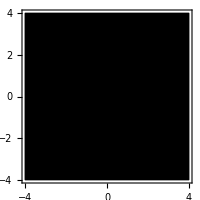

```mathematica
c1=0.7;
c2=3;

σSPSigmoidalR[z_,c1_,c2_]:=(2 c1)/(1+Exp[-c2 z])-c1;
σSPSigmoidal:=σSPSigmoidalR[Re[z],c1,c2]+I σSPSigmoidalR[Im[z],c1,c2];

ComplexPlot3D[σSPSigmoidal,{z,-4-4 I,4+4 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","σSPSigmoidal"},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->250]

ComplexPlot[σSPSigmoidal,{z,-4-4 I,4+4 I},PlotRange->All,ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200]
```

code 10.25

(* The code defines a function `createSplitTanhPlot` to visualize various components (real part, imaginary part, magnitude, and phase) of the Split-Tanh function, which applies the hyperbolic tangent (tanh) separately to the real and imaginary parts of the complex variable z=x+iy. By modularly generating 3D surface plots and slice contour plots for each component over the range [-3,3] for both real and imaginary parts, the function combines these plots for comprehensive visualization. This approach efficiently produces and displays plots for the real part, imaginary part, magnitude, and phase of the Split-Tanh function, allowing for a detailed comparison and understanding of its behavior in the complex plane: *)

```mathematica
createSplitTanhPlot[component_,label_]:=Module[{plot1,slice},znumber=x+I*y;
splitTanh:=Tanh[Re[znumber]]+I*Tanh[Im[znumber]];
plot1=Plot3D[component,{x,-3,3},{y,-3,3},ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"];
slice=SliceContourPlot3D[component,z==0,{x,-3,3},{y,-3,3},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"];
Show[plot1,slice,PlotRange->All,PlotLabel->label,BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->200]]

realSplitTanhPlot=createSplitTanhPlot[Re[splitTanh],"Real Part of split-Tanh(z)"];
imaginarySplitTanhPlot=createSplitTanhPlot[
Im[splitTanh],"Imaginary Part of split-Tanh(z)"
];
magnitudeSplitTanhPlot=createSplitTanhPlot[Abs[splitTanh],"Magnitude of split-Tanh(z)"];
phaseSplitTanhPlot=createSplitTanhPlot[Arg[splitTanh],"Phase of split-Tanh(z)"];

{realSplitTanhPlot,imaginarySplitTanhPlot,magnitudeSplitTanhPlot,phaseSplitTanhPl ot}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,ot phaseSplitTanhPl}

code 10.26

-Graphics3D-

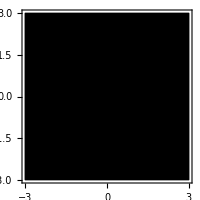

```mathematica
splitTanh:=Tanh[Re[z]]+I*Tanh[Im[z]];

ComplexPlot3D[splitTanh,{z,-3-3 I,3+3 I},PlotRange->All,
AxesLabel->{"Re(z)","Im(z)","SplitTanh(z)"},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->250
]

ComplexPlot[splitTanh,{z,-3-3 I,3+3 I},PlotRange->All,ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200]
```

code 10.27

(* The code defines a function `createSplitSTanhPlot` to visualize various components (real part, imaginary part, magnitude, and phase) of the Split-Sigmoidal Tanh function, which applies a modified tanh transformation separately to the real and imaginary parts of the complex variable z=x+iy. By modularly generating 3D surface plots and slice contour plots for each component over the range [-6,6] for both real and imaginary parts, the function combines these plots for comprehensive visualization. This approach efficiently produces and displays plots for the real part, imaginary part, magnitude, and phase of the Split-Sigmoidal Tanh function, allowing for a detailed comparison and understanding of its behavior in the complex plane: *)

```mathematica
createSplitSTanhPlot[component_,label_]:=Module[{plot1,slice},znumber=x+I*y;
rePart=Tanh[Re[znumber]]/(1-(Re[znumber]-3) Exp[-Re[znumber]]);
imPart=Tanh[Im[znumber]]/(1-(Im[znumber]-3) Exp[-Im[znumber]]);
splitSTanh:=rePart+I imPart;
plot1=Plot3D[
component,{x,-6,6},{y,-6,6},ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"
];

slice=SliceContourPlot3D[component,z==0,{x,-6,6},{y,-6,6},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"];

Show[plot1,slice,PlotRange->All,PlotLabel->label,BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->200]
]

realSplitSTanhPlot=createSplitSTanhPlot[Re[splitSTanh],"Real Part of split-STanh(z)"];
imaginarySplitSTanhPlot=createSplitSTanhPlot[Im[splitSTanh],"Imaginary Part of split-STanh(z)"];
magnitudeSplitSTanhPlot=createSplitSTanhPlot[Abs[splitSTanh],"Magnitude of split-STanh(z)"];
phaseSplitSTanhPlot=createSplitSTanhPlot[Arg[splitSTanh],
"Phase of split-STanh(z)"
];

{realSplitSTanhPlot,imaginarySplitSTanhPlot,magnitudeSplitSTanhPlot,phaseSplitSTa nhPlot}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,nhPlot phaseSplitSTa}

code 10.28

```mathematica
rePart=Tanh[Re[z]]/(1-(Re[z]-3) Exp[-Re[z]]);
imPart=Tanh[Im[z]]/(1-(Im[z]-3) Exp[-Im[z]]);
splitSTanh:=rePart+I imPart;
(*Generate a 3D plot of the Split-Sigmoidal Tanh function over a specified complex range:*)
ComplexPlot3D[splitSTanh,{z,-3-3 I,3+3 I},(*Plot options:*)PlotRange->All,AxesLabel->{"Re(z)","Im(z)","SplitSTanh(z)"},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->250]
ComplexPlot[splitSTanh,{z,-3-3 I,3+3 I},(*Plot options:*)PlotRange->All,ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200]
```

-Graphics3D-

-Graphics-

code 10.29

(* The code defines a function `createSplitCReLUPlot` to visualize various components (real part, imaginary part, magnitude, and phase) of the Split-CReLU function, which applies a Rectified Linear Unit (ReLU) separately to the real and imaginary parts of the complex variable z=x+iy. By modularly generating 3D surface plots and slice contour plots for each component over the range [-6,6] for both real and imaginary parts, the function combines these plots for comprehensive visualization. This approach efficiently produces and displays plots for the real part, imaginary part, magnitude, and phase of the Split-CReLU function, allowing for a detailed comparison and understanding of its behavior in the complex plane: *)

```mathematica
createSplitCReLUPlot[component_,label_]:=Module[{plot1,slice},znumber=x+I*y;
rePart=Max[Re[znumber],0];
imPart=Max[Im[znumber],0];
splitReLU:=rePart+I imPart;
plot1=Plot3D[component,{x,-6,6},{y,-6,6},ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral" ];
slice=SliceContourPlot3D[component,z==0,{x,-6,6},{y,-6,6},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"];
Show[plot1,slice,PlotRange->All,PlotLabel->label,BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->200]]

realSplitCReLUPlot=createSplitCReLUPlot[Re[splitReLU],"Real Part of split-CReLU(z)"];
imaginarySplitCReLUPlot=createSplitCReLUPlot[Im[splitReLU],"Imaginary Part of split-CReLU(z)"];
magnitudeSplitCReLUPlot=createSplitCReLUPlot[Abs[splitReLU],"Magnitude of split-CReLU(z)"];
phaseSplitCReLUPlot=createSplitCReLUPlot[Arg[splitReLU],"Phase of split-CReLU(z)"];

{realSplitCReLUPlot,imaginarySplitCReLUPlot,magnitudeSplitCReLUPlot,phaseSplitCRe LUPlot}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,LUPlot phaseSplitCRe}

code 10.30

-Graphics3D-

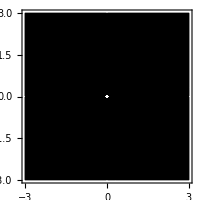

```mathematica
rePart=Max[Re[z],0];
imPart=Max[Im[z],0];
splitReLU:=rePart+I imPart;

ComplexPlot3D[splitReLU,{z,-3-3 I,3+3 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","CReLU(z)"},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->250]

ComplexPlot[splitReLU,{z,-3-3 I,3+3 I},PlotRange->All,ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,
BoxRatios->{1,1,1},ImageSize->200
]
```

code 10.31

(* The code defines a modular function `createSplitQAMPlot` to visualize different components (real part, imaginary part, magnitude, and phase) of the Split-QAM function, which involves a sinusoidal transformation of a complex variable z=x+iy with a slope parameter (alpha). By generating 3D surface plots and slice contour plots for each component over the range [-6,6] for both real and imaginary parts, the function combines these plots for comprehensive visualization. This approach efficiently produces and displays the plots, allowing for a detailed comparison and understanding of the Split-QAM function’s behavior in the complex plane. The final output includes all four generated plots presented together for easy comparison: *)

```mathematica
createSplitQAMPlot[component_,label_]:=Module[{plot1,slice},znumber=x+I*y;
α=0.5;
rePart=Re[znumber]+α Sin[Pi Re[znumber]];
imPart=Im[znumber]+α Sin[Pi Im[znumber]];
SplitQAM:=rePart+I imPart;
plot1=Plot3D[component,{x,-6,6},{y,-6,6},ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"
];

slice=SliceContourPlot3D[component,z==0,{x,-6,6},{y,-6,6},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"];

Show[plot1,slice,PlotRange->All,PlotLabel->label,BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->200]
]

realSplitQAMPlot=createSplitQAMPlot[Re[SplitQAM],"Real Part of split-QAM(z)"];
imaginarySplitQAMPlot=createSplitQAMPlot[Im[SplitQAM],"Imaginary Part of split-QAM(z)"];
magnitudeSplitQAMPlot=createSplitQAMPlot[Abs[SplitQAM],"Magnitude of split-QAM(z)"];
phaseSplitQAMPlot=createSplitQAMPlot[Arg[SplitQAM],"Phase of split-QAM(z)"];

{realSplitQAMPlot,imaginarySplitQAMPlot,magnitudeSplitQAMPlot,phaseSplitQAMPlot}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

code 10.32

```mathematica
Manipulate[Module[{plot1,slice,x,y},znumber=x+I*y;
rePart=Re[znumber]+α Sin[Pi Re[znumber]];
imPart=Im[znumber]+α Sin[Pi Im[znumber]];
SplitQAM:=rePart+I imPart;
plot1=Plot3D[Re[SplitQAM],{x,-6,6},{y,-6,6},ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"
];

slice=SliceContourPlot3D[Re[SplitQAM],z==0,{x,-6,6},{y,-6,6},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"];

Show[plot1,slice,PlotRange->All,PlotLabel->"Real Part of split-QAM(z)",BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->250]
],{{α,0.5,"α"},0.1,2,0.1}
]
```

code 10.33

```mathematica
rePart=Re[z]+α Sin[Pi Re[z]];
imPart=Im[z]+α Sin[Pi Im[z]];
SplitQAM:=rePart+I imPart;

ComplexPlot3D[SplitQAM,{z,-3-3 I,3+3 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","SplitQAM(z)"},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->270]

ComplexPlot[SplitQAM,{z,-3-3 I,3+3 I},PlotRange->All,ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200]
```

-Graphics3D-

-Graphics-

code 10.34

(* The code defines a function `createSplitAVPlot` to visualize various components (real part, imaginary part, magnitude, and phase) of the Split-absolute value (Split-AV)=Split-Hard Tanh function, which applies a custom transformation separately to the real and imaginary parts of the complex variable z=x+iy. By modularly generating 3D surface plots and slice contour plots for each component over the range [-6,6] for both real and imaginary parts, the function combines these plots for comprehensive visualization. This approach efficiently produces and displays plots for the real part, imaginary part, magnitude, and phase of the Split-AV Tanh function, allowing for a detailed comparison and understanding of its behavior in the complex plane: *)

```mathematica
createSplitAVPlot[component_,label_]:=Module[{plot1,slice},znumber=x+I*y;
rePart=1/2 (Abs[Re[znumber]+1]-Abs[Re[znumber]-1]);
imPart=1/2 (Abs[Im[znumber]+1]-Abs[Im[znumber]-1]);
SplitAV:=rePart+I imPart;
plot1=Plot3D[component,{x,-6,6},{y,-6,6},ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"];
slice=SliceContourPlot3D[component,z==0,{x,-6,6},{y,-6,6},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"];
Show[plot1,slice,PlotRange->All,PlotLabel->label,BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->200]]

realSplitAVPlot=createSplitAVPlot[Re[SplitAV],"Real Part of Split-HardTanh(z)"];
imaginarySplitAVPlot=createSplitAVPlot[Im[SplitAV],"Imaginary Part of Split-HardTanh(z)"];
magnitudeSplitAVPlot=createSplitAVPlot[Abs[SplitAV],"Magnitude of Split-HardTanh(z)"];
phaseSplitAVPlot=createSplitAVPlot[Arg[SplitAV],"Phase of Split-HardTanh(z)"];

{realSplitAVPlot,imaginarySplitAVPlot,magnitudeSplitAVPlot,phaseSplitAVPlot}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

code 10.35

```mathematica
rePart=1/2 (Abs[Re[z]+1]-Abs[Re[z]-1]);
imPart=1/2 (Abs[Im[z]+1]-Abs[Im[z]-1]);
SplitAV:=rePart+I imPart;

ComplexPlot3D[
SplitAV,{z,-3-3 I,3+3 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","SplitHardTanh(z)"},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->270
]

ComplexPlot[SplitAV,{z,-3-3 I,3+3 I},PlotRange->All,ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200]
```

-Graphics3D-

-Graphics-

code 10.36

(* The code defines a function `createAFTAFPlot` that generates 3D surface plots and slice contour plots for different components (real part, imaginary part, magnitude, and phase) of the Amplitude-Phase-Type Activation Function (AFTAF), given by AFTAF(z)= tanh(|z|) exp(i arg(z)). The function takes the component to be plotted and a label, then generates and combines the 3D and slice plots for the specified component. By calling `createAFTAFPlot` for each component, the code efficiently produces and displays plots for the real part, imaginary part, magnitude, and phase of the AFTAF function, allowing comprehensive

```mathematica
createAFTAFPlot[component_,label_]:=Module[{plot1,slice},znumber=x+I*y;
AFTAF:=Tanh[Abs[znumber]] Exp[I Arg[znumber]];
plot1=Plot3D[component,{x,-3,3},{y,-3,3},ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"];

slice=SliceContourPlot3D[component,z==0,{x,-3,3},{y,-3,3},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"];

Show[plot1,slice,PlotRange->All,PlotLabel->label,BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->200]
]

realAFTAFPlot=createAFTAFPlot[Re[AFTAF],"Real Part of APTF(z)"];
imaginaryAFTAFPlot=createAFTAFPlot[Im[AFTAF],"Imaginary Part of APTF(z)"];
magnitudeAFTAFPlot=createAFTAFPlot[Abs[AFTAF],"Magnitude of APTF(z)"];
phaseAFTAFPlot=createAFTAFPlot[
Arg[AFTAF],"Phase of APTF(z)"
];

{realAFTAFPlot,imaginaryAFTAFPlot,magnitudeAFTAFPlot,phaseAFTAFPlot}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

code 10.37

-Graphics3D-

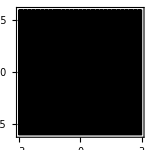

```mathematica
ComplexPlot3D[Tanh[Abs[z]] Exp[I Arg[z]],{z,-3-3 I,3+3 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","APTF(z)"},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200]

ComplexPlot[
Tanh[Abs[z]] Exp[I Arg[z]],{z,-3-3 I,3+3 I},PlotRange->All,ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->150
]
```

code 10.38

(* The code defines a function createAPSFPlot that generates 3D surface plots and slice contour plots for different components (real part, imaginary part, magnitude, and phase) of the Amplitude-Phase Sigmoidal Function (APSF) defined as PASF=(b/(a*b+Abs[z]))*z with parameters a and b. The function takes the component to be plotted and a label, then generates and combines the 3D and slice plots for the specified component. By calling createAPSFPlot for each component, the code efficiently produces and displays plots for the real part, imaginary part, magnitude, and phase of the APSF function, allowing comprehensive visualization and comparison of these aspects over a specified: *)

```mathematica
createAPSFPlot[component_,label_]:=Module[{plot1,slice},znumber=x+I*y;
a=1;
b=1;
PASF:=(b/(a*b+Abs[znumber]))*znumber;
plot1=Plot3D[component,{x,-6,6},{y,-6,6},ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},
Lighting->"Neutral"
];

slice=SliceContourPlot3D[component,z==0,{x,-6,6},{y,-6,6},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"];

Show[plot1,slice,PlotRange->All,PlotLabel->label,BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->200]
]

realAPSFPlot=createAPSFPlot[Re[PASF],"Real Part of APSF"];
imaginaryAPSFPlot=createAPSFPlot[Im[PASF],"Imaginary Part of APSF"];
magnitudeAPSFPlot=createAPSFPlot[Abs[PASF],"Magnitude of APSF"];
phaseAPSFPlot=createAPSFPlot[Arg[PASF],"Phase of APSF"];

{realAPSFPlot,imaginaryAPSFPlot,magnitudeAPSFPlot,phaseAPSFPlot}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

cdoe 10.39

-Graphics3D-

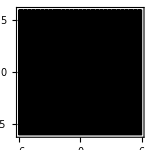

```mathematica
a=2;
b=1;

PASF:=(b/(a*b+Abs[z]))*z

ComplexPlot3D[PASF,{z,-6-6 I,6+6 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","APSF"},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200]

ComplexPlot[PASF,{z,-6-6 I,6+6 I},PlotRange->All,ColorFunction->"CyclicLogAbsArg",
PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->150
]
```

code 10.40

(* The code provides an interactive interface for exploring the Amplitude-Phase Sigmoidal Function in both 3D and 2D plots. Users can dynamically adjust the parameters a and b to observe the impact on the function’s behavior in real-time. The side-by-side display of the 3D and 2D plots allows for a comprehensive understanding of the function’s characteristics: *)

```mathematica
Manipulate[PASF:=(b/(a*b+Abs[z]))*z;
Row[{ComplexPlot3D[PASF,{z,-6-6 I,6+6 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","APSF"},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200],ComplexPlot[PASF,{z,-6-6 I,6+6 I},PlotRange->All,ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->150]}],{{a,2,"a"},0.1,5,0.1},{{b,1,"b"},0.1,5,0.1}]
```

code 10.41

(* The code aims to visualize various components of the complex cardioid activation function, defined as cCardioid(z)= 1/2 (1+ cos(arg(z))) z, in the complex plane where z=x+i y. It defines this function and uses a reusable function `createCardioidPlot` to generate 3D surface plots and slice contour plots for the real part,imaginary part, magnitude, and phase of the function. Each plot displays the specified component over a specified range, combining both 3D and contour visualizations to provide a comprehensive view. The final output is a collection of four plots, each highlighting a different component of the complex cardioid function: *)

```mathematica
znumber=x+I*y;

cCardioid:=1/2 (1+Cos[Arg[znumber]])*znumber

createCardioidPlot[component_,label_]:=Module[{plot1,slice},plot1=Plot3D[component,{x,-6,6},{y,-6,6},ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"];
slice=SliceContourPlot3D[component,z==0,{x,-6,6},
{y,-6,6},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"
];

Show[plot1,slice,PlotRange->All,PlotLabel->label,BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->200]
]

realCardioidPlot=createCardioidPlot[Re[cCardioid],"Real Part of Complex Cardioid"];
imaginaryCardioidPlot=createCardioidPlot[Im[cCardioid],"Imaginary Part of Complex Cardioid"];
magnitudeCardioidPlot=createCardioidPlot[Abs[cCardioid],"Magnitude of Complex Cardioid"];
phaseCardioidPlot=createCardioidPlot[Arg[cCardioid],"Phase of Complex Cardioid"];

{realCardioidPlot,imaginaryCardioidPlot,magnitudeCardioidPlot,phaseCardioidPlot}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

code 10.42

-Graphics3D-

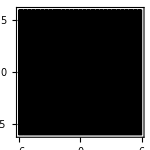

```mathematica
CCardioid:=1/2 (1+Cos[Arg[z]])*z

ComplexPlot3D[CCardioid,{z,-6-6 I,6+6 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","CCardioid"},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200]

ComplexPlot[CCardioid,{z,-6-6 I,6+6 I},PlotRange->All,ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->150]
```

code 10.43

(* The code aims to visualize various components of the complex modReLU function, defined as a piecewise function operating on the magnitude and phase of the complex variable z=x+iy. It defines this function and uses a reusable function `createModReLUPlot` to generate 3D surface plots and slice contour plots for the real part, imaginary part, magnitude, and phase of the function. Each plot displays the specified component over a specified range, combining both 3D and contour visualizations to provide a comprehensive view. The final output is a collection of four plots, each highlighting a different component of the complex modReLU function: *)

```mathematica
znumber=x+I*y;
b=-0.7;

modReLU:=Piecewise[{{(1+b/Abs[znumber]) znumber,Abs[znumber]+b>=0},{0,Abs[znumber]+b<0}}]

createModReLUPlot[component_,label_]:=Module[{plot1,slice},plot1=Plot3D[component,{x,-2,2},{y,-2,2},ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"];
slice=SliceContourPlot3D[component,z==0,{x,-2,2},{y,-2,2},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"];
Show[plot1,
slice,PlotRange->All,PlotLabel->label,BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->200
]
]

realModReLUPlot=createModReLUPlot[Re[modReLU],"Real Part of modReLU(z)"];
imaginaryModReLUPlot=createModReLUPlot[Im[modReLU],"Imaginary Part of modReLU(z)"];
magnitudeModReLUPlot=createModReLUPlot[Abs[modReLU],"Magnitude of modReLU(z)"];
phaseModReLUPlot=createModReLUPlot[Arg[modReLU],"Phase of modReLU(z)"];

{realModReLUPlot,imaginaryModReLUPlot,magnitudeModReLUPlot,phaseModReLUPlot}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

code 10.44

(* The code defines a function `createComplexPlots` that generates both 3D and 2D complex plots of the modReLU function, which is parameterized by b. This function modularly creates the modReLU function and produces visualizations using `ComplexPlot3D` and `ComplexPlot` over a specified complex range. By calling `createComplexPlots` with different values of b (e.g., b=-0.7 and b=2), the code efficiently generates and displays the plots, allowing for a comparison of the function’s behavior under different parameters: *)

```mathematica
createComplexPlots[b_]:=Module[{modReLU},modReLU:=Piecewise[{{(1+b/Abs[z]) z,Abs[z]+b>=0},{0,Abs[z]+b<0}}];
plot3D=ComplexPlot3D[modReLU,{z,-6-6 I,6+6 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","modReLU"},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200];
plot2D=ComplexPlot[modReLU,{z,-6-6 I,6+6 I},PlotRange->All,ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->150];
{plot3D,plot2D}]

plotsNeg07=createComplexPlots[-0.7];

plots2=createComplexPlots[2];

{plotsNeg07,plots2}
```

{{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-}}

code 10.45

(* The code defines a function `createComplexPlots` that generates both 3D and 2D complex plots of the modReLU function, which is parameterized by b. It uses `Manipulate` to create an interactive interface allowing users to dynamically adjust the parameter b and observe the changes in the function’s behavior in real- time. The function `createComplexPlots` modularly defines the modReLU function, generates visualizations using `ComplexPlot3D` and `ComplexPlot`, and returns both plots: *)

```mathematica
createComplexPlots[b_]:=Module[{modReLU,plot3D,plot2D},modReLU:=Piecewise[{{(1+b/Abs[z]) z,Abs[z]+b>=0},{0,Abs[z]+b<0}}];
plot3D=ComplexPlot3D[modReLU,{z,-6-6 I,6+6 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","modReLU"},ColorFunction->"CyclicLogAbsArg",
PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200
];

plot2D=ComplexPlot[modReLU,{z,-6-6 I,6+6 I},PlotRange->All,ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->150];
{plot3D,plot2D}
]

Manipulate[Module[{plots},plots=createComplexPlots[b];
Column[plots]],{{b,-0.7},-3,3,0.1,Appearance->"Labeled"},ControlPlacement->Top]
```

code 10.46

(* The code aims to visualize various components of the complex hyperbolic tangent function tanh(z), where z=x+iy, in the complex plane. It defines this function and uses a reusable function `createTanhPlot` to generate 3D surface plots and slice contour plots for the real part, imaginary part, magnitude, and phase of the function. Each plot displays the specified component over a specified range, combining both 3D and contour visualizations to provide a comprehensive view. The final output is a collection of four plots, each highlighting a different component of the complex hyperbolic tangent function: *)

```mathematica
z=x+I*y;

tanhz=Tanh[z];

createTanhPlot[component_,label_]:=Module[{plot1,slice},plot1=Plot3D[component,{x,-3,3},{y,-3,3},ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"];
slice=SliceContourPlot3D[component,z==0,{x,-3,3},{y,-3,3},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"];
Show[plot1,slice,PlotRange->All,PlotLabel->label,BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->200
]]

realTanhPlot=createTanhPlot[Re[tanhz],"Real Part of Tanh(z)"];
imaginaryTanhPlot=createTanhPlot[Im[tanhz],"Imaginary Part of Tanh(z)"];
magnitudeTanhPlot=createTanhPlot[Abs[tanhz],"Magnitude of Tanh(z)"];
phaseTanhPlot=createTanhPlot[Arg[tanhz],"Phase of Tanh(z)"];

{realTanhPlot,imaginaryTanhPlot,magnitudeTanhPlot,phaseTanhPlot}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

code 10.47

```mathematica
ComplexPlot3D[Tanh[z],{z,-3-3 I,3+3 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","Tanh[z]"},ColorFunction->"CyclicLogAbs",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200]

ComplexPlot[Tanh[z],{z,-3-3 I,3+3 I},PlotRange->All,ColorFunction->"CyclicLogAbs",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->150]
```

-Graphics3D-

-Graphics-

code 10.48

(* The code aims to visualize various components of the complex sigmoid function sigma(z)= 1/(1+Exp[-z]) in the complex plane, where z=x+i y. It defines this function and uses a reusable function `createSigmoidPlot` to generate 3D surface plots and slice contour plots for the real part, imaginary part, magnitude, and phase of the function. Each plot displays the specified component over a specified range, combining both 3D and contour visualizations to provide a comprehensive view. The final output is a collection of four plots, each highlighting a different component of sigma(z): *)

```mathematica
znumber=x+I*y;

sigmoid:=1/(1+Exp[-znumber])

createSigmoidPlot[component_,label_]:=Module[{plot1,slice},
plot1=Plot3D[component,{x,-6,6},{y,-6,6},ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"];

slice=SliceContourPlot3D[component,z==0,{x,-6,6},{y,-6,6},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"];

Show[plot1,slice,PlotRange->All,PlotLabel->label,BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->200]
]

realSigmoidPlot=createSigmoidPlot[Re[sigmoid],"Real Part of sigmoid(z)"];
imaginarySigmoidPlot=createSigmoidPlot[Im[sigmoid],"Imaginary Part of sigmoid(z)"];
magnitudeSigmoidPlot=createSigmoidPlot[Abs[sigmoid],"Magnitude of sigmoid(z)"];
phaseSigmoidPlot=createSigmoidPlot[Arg[sigmoid],"Phase of sigmoid(z)"];

{realSigmoidPlot,imaginarySigmoidPlot,magnitudeSigmoidPlot,phaseSigmoidPlot}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

code 10.49 (Not Working)

```mathematica
sigmoid1[z_]=1/(1+Exp[-z]);

ComplexPlot3D[sigmoid1[z],{z,-6-6 I,6+6 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","Sigmoidz)"},ColorFunction->"CyclicLogAbs",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200]

ComplexPlot[sigmoid1[z],{z,-6-6 I,6+6 I},PlotRange->All,ColorFunction->"CyclicLogAbs",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->150]
```

-Graphics3D-

-Graphics-

code 10.50

(* The code aims to visualize different aspects of the complex exponential function exp(z) in the complex plane, where z=x+i y. It defines the function and then uses a reusable function `createPlot` to generate 3D surface plots and slice contour plots for the real part, imaginary part, magnitude, and phase of exp(z). Each plot displays the specified component over a specified range, combining both 3D and contour visualizations to provide a comprehensive view. The final output is a collection of four plots, each highlighting a different component of exp(z): *)

```mathematica
z=x+I*y;

expz=Exp[z];

createPlot[component_,label_]:=Module[{plot1,slice},plot1=Plot3D[component,{x,-6,6},{y,-6,6},(*Plot options:*)ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"];
slice=SliceContourPlot3D[component,z==0,{x,-6,6},{y,-6,6},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"];

Show[plot1,slice,PlotRange->All,PlotLabel->label,BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->200]
]

realPlot=createPlot[Re[expz],"Real Part of FCExpExp(z)"];
imaginaryPlot=createPlot[Im[expz],"Imaginary Part of FCExp(z)"];
magnitudePlot=createPlot[Abs[expz],"Magnitude of FCExp(z)"];
phasePlot=createPlot[Arg[expz],"Phase of FCExpExp(z)"];

{realPlot,imaginaryPlot,magnitudePlot,phasePlot}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

code 10.51

```mathematica
ComplexPlot3D[Exp[z],{z,-6-6 I,6+6 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","Exp(z)"},ColorFunction->"CyclicLogAbs",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200]

ComplexPlot[Exp[z],{z,-6-6 I,6+6 I},PlotRange->All,ColorFunction->"CyclicLogAbs",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->150]
```

-Graphics3D-

-Graphics-

code 10.52

(* The code defines and visualizes the `zReLU` activation function for a complex variable z=x+iy, which returns z if both the real and imaginary parts are positive, and 0 otherwise. It introduces a reusable function `createPlot` to generate and display 3D surface plots and slice contour plots for the real part, imaginary part, magnitude, and phase of the `zReLU` function. The generated plots are displayed together, allowing for a comprehensive examination of the `zReLU` function’s behavior across different components in the complex plane: *)

```mathematica
znumber=x+I*y;

zReLU:=Piecewise[{{znumber,Re[znumber]>0&&Im[znumber]>0},{0,True}}]

createPlot[part_,label_]:=Module[{plot,slice},plot=Plot3D[part[zReLU],{x,-6,6},{y,-6,6},ClippingStyle->None,AxesLabel->{"Re(z)","Im(z)"},MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"];
slice=SliceContourPlot3D[part[zReLU],z==0,{x,-6,6},{y,-6,6},{z,-1,1},Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"];
Show[plot,slice,PlotRange->All,PlotLabel->label,BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->200]]

realzReLU=createPlot[Re,"Real Part of zReLU(z)"];
imaginaryzReLU=createPlot[Im,"Imaginary Part of zReLU(z)"];
magnitudezReLU=createPlot[Abs,"Magnitude of zReLU(z)"];
phasezReLU=createPlot[Arg,"Phase of zReLU(z)"];

{realzReLU,imaginaryzReLU,magnitudezReLU,phasezReLU}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

code 10.53

```mathematica
zReLU:=Piecewise[{{z,Re[z]>0&&Im[z]>0},{0,True}}]

ComplexPlot3D[zReLU,{z,-6-6 I,6+6 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","zReLU(z)"},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200]
```

-Graphics3D-

code 10.54

```mathematica
z3ReLU:=Piecewise[{{z,Re[z]>0||Im[z]>0},{0,True}}]

ComplexPlot3D[z3ReLU,{z,-6-6 I,6+6 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","z3ReLU(z)"},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200]
```

-Graphics3D-

code 10.55

(* The code creates an interactive environment using the `Manipulate` function, allowing users to dynamically adjust the parameters α, α1, α2, and α3 for two complex-valued activation functions defined using piecewise conditions. The first function, σzPReLU, changes its value based on whether both the real and imaginary parts of the complex variable z are positive, while the second function, σz3PReLU, considers different cases for combinations of positive and negative real and imaginary parts. The code generates 3D plots for both functions, displaying their behavior over a specified range of complex values. By manipulating the sliders, users can observe how the surfaces of these functions change, enhancing their understanding of the impact of parameter variations on complex activation functions: *)

```mathematica
Manipulate[{σzPReLU:=Piecewise[{{z,Re[z]>0&&Im[z]>0},{α z,True}}];
σz3PReLU:=Piecewise[{{z,Re[z]>0&&Im[z]>0},{α1 z,Re[z]<=0&&Im[z]>0},{α2 z,Re[z]>0&&Im[z]<=0},{α3 z,True}}];
plot1=ComplexPlot3D[σzPReLU,{z,-6-6 I,6+6 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","zPReLU(z)"},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200];
plot2=ComplexPlot3D[σz3PReLU,{z,-6-6 I,6+6 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)","z3PReLU(z)"},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200];
Row[{plot1,plot2}]},{{α,0.5,"α for σzPReLU"},0,1,0.1},{{α1,0.5,"α1 for σz3PReLU"},0,1,0.1},{{α2,0.7,"α2 for σz3PReLU"},0,1,0.1},{{α3,0.9,"α3 for σz3PReLU"},0,1,0.1}]
```

code 10.56

(* The code defines a function `generatePlots` to create combined 3D and slice contour plots of the magnitudes of various complex functions. The function takes a mathematical function and its label as inputs, generating 3D plots with specific visual styles and labels for the real and imaginary parts of the complex variable. It also creates slice contour plots at `z=0` to show the function’s behavior in that plane. The combined plots are displayed using the `Show` function. The code then defines a list of functions (`Tan`, `Tanh`, `ArcTan`, `ArcTanh`, `Sin`, `Sinh`, `ArcSin`, `ArcCos`, `ArcSinh`) with their labels, and iterates over this list to generate and display the corresponding plots for each function: *)

```mathematica
generatePlots[func_,label_]:=Module[{z,plot1,slice},z=x+I*y;
plot1=Plot3D[Abs[func[z]],{x,-3,3},{y,-3,3},AxesLabel->{"Re(z)","Im(z)"},ClippingStyle->None,MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"];
slice=SliceContourPlot3D[Abs[func[z]],zz==0,{x,-3,3},{y,-3,3},{zz,-1,1},Contours->15,
Axes->False,PlotPoints->50,PlotRangePadding->0,ColorFunction->"Rainbow"
];

Show[plot1,slice,PlotRange->All,PlotLabel->"Magnitude of "<>label,BoxRatios->{1,1,1},FaceGrids->{Back,Left},ImageSize->200]
]

functions={{Tan,"Tan(z)"},{Tanh,"Tanh(z)"},{ArcTan,"ArcTan(z)"},{ArcTanh,"ArcTanh(z)"},{Sin,"Sin(z)"},{Sinh,"Sinh(z)"},{ArcSin,"ArcSin(z)"},{ArcCos,"ArcCos(z)"},{ArcSinh,"ArcSinh(z)"}};

plots=Table[generatePlots[func[[1]],func[[2]]],{func,functions}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

code 10.57 (Not Working)

(* The code defines a list of complex functions along with their labels and uses Mathematica’s `ComplexPlot3D` to generate 3D visualizations for each function over a specified range in the complex plane. By iterating over the list of functions with a `Table` construct, it produces a series of 3D plots that illustrate the real and imaginary components of the functions, facilitating better understanding and analysis of their behaviors: *)

```mathematica
functions={{Tan[z],"Tan(z)"},{Tanh[z],"Tanh(z)"},{ArcTan[z],"ArcTan(z)"},{ArcTanh[z],"ArcTanh(z)"},{Sin[z],"Sin(z)"},{Sinh[z],"Sinh(z)"},{ArcSin[z],"ArcSin(z)"},{ArcCos[z],"ArcCos(z)"},{ArcSinh[z],"ArcSinh(z)"}};

plots=Table[ComplexPlot3D[func[[1]],{z,-3-3 I,3+3 I},PlotRange->All,AxesLabel->{"Re(z)","Im(z)",func[[2]]},ColorFunction->"CyclicLogAbs",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200],{func,functions}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

code 10.58 (Not Working)

(* The code defines a list of complex functions along with their labels and uses Mathematica’s `ComplexPlot` to generate 2D visualizations for each function over a specified range in the complex plane. By iterating over the list of functions with a `Table` construct, it produces a series of 2D Complex plots, facilitating better understanding and analysis of their behaviors: *)

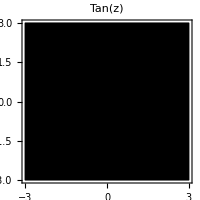
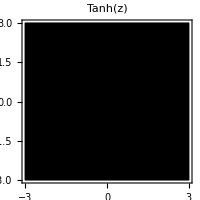
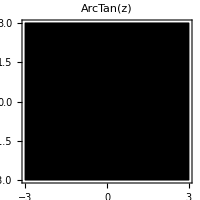
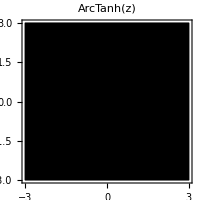
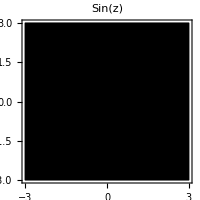
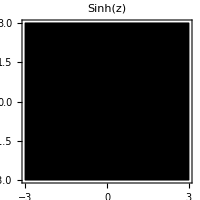
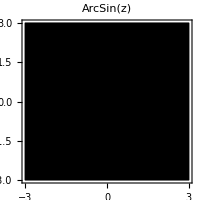
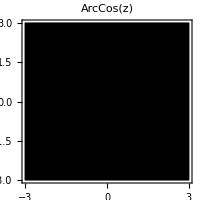

```mathematica
functions={{Tan[z],"Tan(z)"},{Tanh[z],"Tanh(z)"},{ArcTan[z],"ArcTan(z)"},{ArcTanh[z],"ArcTanh(z)"},{Sin[z],"Sin(z)"},{Sinh[z],"Sinh(z)"},{ArcSin[z],"ArcSin(z)"},{ArcCos[z],"ArcCos(z)"},{ArcSinh[z],"ArcSinh(z)"}};

plots=Table[ComplexPlot[func[[1]],{z,-3-3 I,3+3 I},PlotRange->All,PlotLabel->func[[2]],ColorFunction->"CyclicLogAbs",PlotLegends->Automatic,BoxRatios->{1,1,1},ImageSize->200],{func,functions}]
```